## Halbach Array in Radia

```mathematica
(* Initialize Radia*)
<<Radia`;
```

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

```mathematica
createWedge[npts_,din_,dout_,θmin1_,θmax1_]:=Module[{},
poly={};
(* initialize constants *)
θmin=θmin1*Pi/180 ;
θmax=θmax1*Pi/180;
dθ=(θmax-θmin)/npts;
poly={};
(* make innner cirlce *)
For[n=0,n≤npts,n++,
θ=θmin+n*dθ;
AppendTo[poly,din/2*{Cos[θ],Sin[θ]}]]
(* make first connecting line *)
AppendTo[poly,dout/2*{Cos[θ],Sin[θ]}];
(* make outer circle *)
For[n=0,n≤npts,n++,
θ=θmax-(θmax-θmin)/npts*n;
AppendTo[poly,dout/2*{Cos[θ],Sin[θ]}]];
(* close the polygon *)
θ=θmin;
AppendTo[poly,din/2*{Cos[θ],Sin[θ]}]
];
```

```mathematica
Nwedge=12;
din=25.4;
dout= 25.4 * 2;
(*zoffset=0;*)
dz=25.4;
Mr=1.0;
magmat=RadMatNdFeB[];
makeKstage[KK_,zoff_,ϕrot_,cnt_]:=Module[{},
(* make wedge outlines *)
Print["KK = ", KK];
ϕ=2Pi/Nwedge(1-1/2);
Print["ϕ_1 = ", ϕ];
Print["Mvec, pre-rotation: ========>",Mvec=Mr{Cos[KK ϕ],Sin[KK ϕ],0}];
allpolys={};
For[w=1,w≤Nwedge,w++,
createWedge[1,din,dout,360/Nwedge*(w-1),360/Nwedge*w];
AppendTo[allpolys,poly[[1;;-2]]];
ϕ=2Pi/Nwedge(w-1/2);
Mvec=Mr{Cos[KK ϕ],Sin[KK ϕ],0};
rot={{Cos[ϕrot],Sin[ϕrot],0},{-Sin[ϕrot],Cos[ϕrot],0},{0,0,1}};
Mvec=rot.Mvec;
Print["Mvec, rotated: ",Mvec];
obj=radObjThckPgn[zoff,dz,allpolys[[w]],"z",Mvec];
(*radMatApl[obj,magmat];*)
radObjAddToCnt[cnt,{obj}]
];
];
radUtiDelAll[];
stage=radObjCnt[{}];
makeKstage[4,0,Pi/2,stage]
```

KK = 4

ϕ_1 = π/12

Mvec, pre-rotation: ========>{0.5,0.866025,0.}

Mvec, rotated: {0.866025,-0.5,0.}

Mvec, rotated: {0.,1.,0.}

Mvec, rotated: {-0.866025,-0.5,0.}

Mvec, rotated: {0.866025,-0.5,0.}

Mvec, rotated: {0.,1.,0.}

Mvec, rotated: {-0.866025,-0.5,0.}

Mvec, rotated: {0.866025,-0.5,0.}

Mvec, rotated: {0.,1.,0.}

Mvec, rotated: {-0.866025,-0.5,0.}

Mvec, rotated: {0.866025,-0.5,0.}

Mvec, rotated: {0.,1.,0.}

Mvec, rotated: {-0.866025,-0.5,0.}

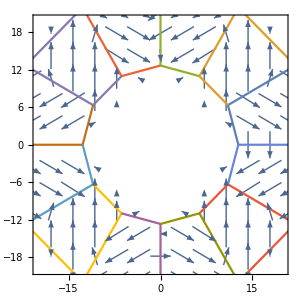

```mathematica
zoff=0;
Mplot=Table[{{x,y},{radFld[stage,"mx",{x,y,zoff}],radFld[stage,"my",{x,y,zoff}]}},{x,-25,25,1},{y,-25,25,1}];
p1=ListVectorPlot[Mplot,AspectRatio->1,ImageSize->300,ColorFunction->"Rainbow",PlotLegends->Automatic];
p2=ListPlot[allpolys,Joined->True];
Show[p1,p2,PlotRange->{{-20,20},{-20,20}}]
```

```mathematica
(* Special options for the Plot[] *)
RadPlot3DOptions[];
(* save the geometry in "dr" *)
dr = radObjDrw[stage];
(* draw the geometry *)
Show[Graphics3D[dr],FrameLabel->{"X","Y","Z"}]
```

-Graphics3D-

-Graphics3D-

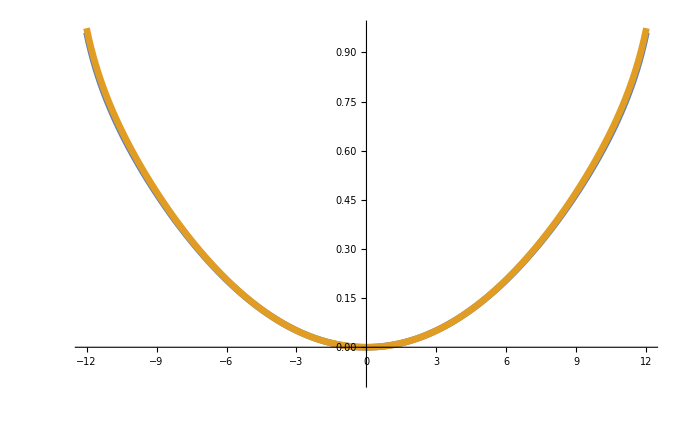

```mathematica
zoffset=0;
xlim=12;
BnormXcut=Table[{x,Sqrt[radFld[stage,"bx",{x,0,zoffset}]^2+radFld[stage,"by",{x,0,zoffset}]^2+radFld[stage,"bz",{x,0,zoffset}]^2]},{x,-xlim,xlim,0.1}];
BnormYcut=Table[{x,Sqrt[radFld[stage,"bx",{0,x,zoffset}]^2+radFld[stage,"by",{0,x,zoffset}]^2+radFld[stage,"bz",{0,x,zoffset}]^2]},{x,-xlim,xlim,0.1}];
ListPlot[{BnormXcut,BnormYcut},Joined->True,PlotStyle->{Thickness[0.007]},PlotRange->{-0.1,All}]
```

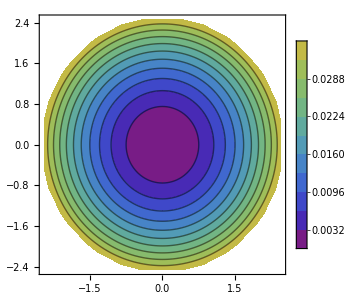

```mathematica
zoff=0;
contourKstage=Table[{x,y,
If[Abs[y]<Sqrt[2.5^2-x^2],Sqrt[radFld[stage,"hx",{x,y,zoff}]^2+radFld[stage,"hy",{x,y,zoff}]^2+radFld[stage,"hz",{x,y,zoff}]^2],Infinity]},{x,-2.5,2.5,0.05},{y,-2.5,2.5,0.05}];
contourKstage=ArrayReshape[contourKstage,{Dimensions[contourKstage][[1]]*Dimensions[contourKstage][[2]],3}];
ListContourPlot[contourKstage,Contours->10,AspectRatio->1,ImageSize->300,ColorFunction->ColorData[{"Rainbow",{0,1.5}}],PlotLegends->Automatic]
```

```mathematica
zoff = 0;
R = 25.4;
m=50;
bMatrix=Table[radFld[stage,"b",{x, y, z}], {x, -R/2, R/2, R/(m-1)}, {y, -R/2, R/2, R/(m-1)}, {z, -R/2, R/2, R/(m-1)}];
normbMatrix=Table[Sqrt[radFld[stage,"bx",{x, y, z}]^2 + radFld[stage,"by",{x, y, z}]^2 +radFld[stage,"bz",{x, y, z}]^2], {x, -R/2, R/2, R/(m-1)}, {y, -R/2, R/2, R/(m-1)}, {z, -R/2, R/2, R/(m-1)}];
SetDirectory["/Users/andrewwinnicki/Desktop/Andrew/2019-2020/Doyle Lab/Modeling Magnetic Lens/magnetic_lens_monte_carlo/b_matrix"];
Export["bMatrix_"<>ToString[m]<>".fits",bMatrix]; 
Export["normbMatrix_"<>ToString[m]<>".fits",normbMatrix];
```

```mathematica
71.1119/(6.0221409*^23)*1/1000
```

1.18084×10^-25

```mathematica
(*plot the b-field against the z-axis; choose a ring and then calculate the b-field about that b-field and plot against the z-axis*)
radius=25.4 / 4;
(*calculate magnitude of b-field*)
θSteps = 100;
meanFieldAtZ={};
(*loop over z-steps along the axial bore of magnet*)
For[zPos=-R-50,zPos<R+50,zPos+=R/(m-1),
(*calculate the b-field at each point, add to an array*)
fieldAtRing=Table[Norm[radFld[stage, "b", {radius*Cos[θ], radius*Sin[θ], zPos}]],{θ, 0, 2*π,2*π/θSteps}];
AppendTo[meanFieldAtZ,Mean[fieldAtRing]];
];
```

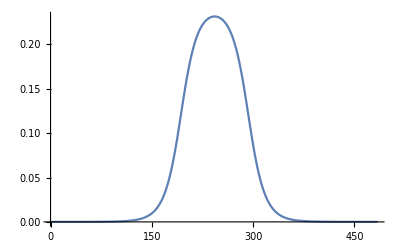

```mathematica
(*plot results*)
zScan=Subdivide[-R-50,R+50,483];
Show[ListLinePlot[meanFieldAtZ]]
```

```mathematica
Length[meanFieldAtZ]
Length[Subdivide[-R-50,R+50,483]]
```

484

484